# Code

```mathematica
importALPSGenes[filename_]:=Select[Import[filename,"Table"], Length[#] == geneCount&]
```

```mathematica
importALPSOut[filename_] := Select[Import[filename,"Table"], Length[#] == 3&]
```

```mathematica
importGenesFromRun[resultName_, expName_, runNo_] := Module[{file},
file= Last[FileNames[resultName <> "/" <> ToString[expName] <> "/" <> ToString[runNo] <> "-*.pop"]];
importALPSGenes[file]]
```

```mathematica
importResults[directoryName_] := Module[{files},
files = FileNames["output.txt",{directoryName},3];
combineResults[Map[{FileBaseName[DirectoryName[#,2]] , importALPSOut[#]}&, files]]]
```

```mathematica
chartOfResults[directoryName_String] := chartOfResults[importResults[directoryName]]
```

```mathematica
chartOfResults[res_List] := Module[{},
BarChart[Map[Mean,values[res]], 
	ChartLegends -> keys[res], ChartStyle -> "DarkRainbow"]]
```

```mathematica
combineResultsHelper[splitResult_] := Module[{name, justData},
name = splitResult[[1,1]];
justData = Map[#[[2]]&, splitResult];
name ->  Map[#[[-1,-1]]&, justData]]
```

```mathematica
combineResults[results_] := Module[{},
Map[combineResultsHelper, SplitBy[results, #[[1]]&]]]
```

```mathematica
indexOfMinimum[fun_, inputs_] := Module[{outputs, min},
outputs = Map[fun, inputs];
min = Min[outputs];
Flatten[Position[outputs, min]]]
```

```mathematica
indexOfMaximum[fun_, inputs_] := Module[{outputs, min},
outputs = Map[fun, inputs];
min = Max[outputs];
Flatten[Position[outputs, min]]]
```

```mathematica
importMinGene[filename_, fitnessForGene_] := Module[{genes, index,  indexes},
genes = importALPSGenes[filename];
indexes = indexOfMinimum[fitnessForGene, genes];
If[Length[indexes] > 1,
Message[importMinGene::notuniq]];
index = First[indexes];
genes[[index]]]
```

```mathematica
importMaxGene[filename_, fitnessForGene_] := Module[{genes, index,  indexes},
genes = importALPSGenes[filename];
indexes = indexOfMaximum[fitnessForGene, genes];
If[Length[indexes] > 1,
Message[importMaxGene::notuniq]];
index = First[indexes];
genes[[index]]]
```

# Read Results

```mathematica
<<loadall`
```

```mathematica
loadall[];
```

```mathematica
link = Install["run-simulation-mlink"];
```

```mathematica
Uninstall[link]
```

/Users/shane/School/sussex/thesis/code/src/run-simulation-mlink

```mathematica
Clear[runSimulationMlink]
```

```mathematica
target = {0, 0.1}
```

{0,0.1}

```mathematica
fitness = fitnessToTarge
```

```mathematica
fitness = fitnessToTarget[#, target, Ao, 1]&;
fitnessData = fitnessToTargetData[#, target, Ao, 1]&;
```

```mathematica
fitness = fitnessToTarget[#, target, Ap, 1]&;
fitnessData = fitnessToTargetData[#, target, Ap, 1]&;
```

```mathematica
fitness = fitnessForSpeed[#, Bp, 1]&;
fitnessData = fitnessForSpeedData[#, Bp, 1]&;
```

```mathematica
fitness = fitnessForSpeed[#, Ap, 1]&;
fitnessData = fitnessForSpeedData[#, Ap, 1]&;
```

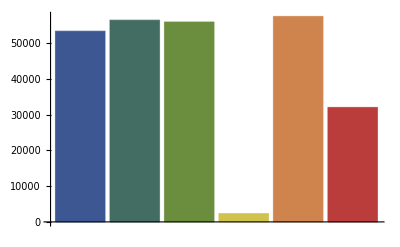
-Graphics--Graphics- | An-t1-l0
-Graphics- | Ao-t1-l0
-Graphics- | Ap-t1-l0
-Graphics- | Bn-t1-l0
-Graphics- | Bo-t1-l0
-Graphics- | Bp-t1-l0

```mathematica
chartOfResults["res9p-target"]
```

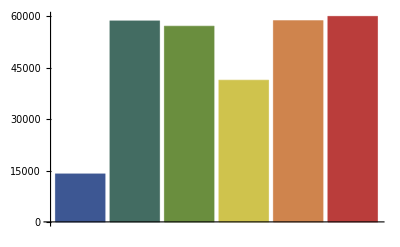
-Graphics--Graphics- | An-t1-l0
-Graphics- | Ao-t1-l0
-Graphics- | Ap-t1-l0
-Graphics- | Bn-t1-l0
-Graphics- | Bo-t1-l0
-Graphics- | Bp-t1-l0

```mathematica
chartOfResults["res8p-target"]
```

```mathematica
importResults["res8p-target"]
```

{An-t1-l0→{14000,14000,14000,14000,14000},Ao-t1-l0→{58680,58680,58680,58680,58680},Ap-t1-l0→{57131,57131,57131,57131,57131},Bn-t1-l0→{41363,41363,41363,41363,41363},Bo-t1-l0→{58757,58757,58757,58757,58757},Bp-t1-l0→{59998,59998,59998,59998,59998}}

```mathematica
importResults["res9p-target"]
```

{An-t1-l0→{53339},Ao-t1-l0→{56420},Ap-t1-l0→{55910},Bn-t1-l0→{2326},Bo-t1-l0→{57461},Bp-t1-l0→{32012}}

```mathematica
gene = importMinGene["res9p-target//Bp-t1-l0/r1/pop-phaseFINAL.pop", fitnessToTarget[#, Bp, 4]&]
```

runSimulationMlink::errnan: Saw NaN at time 4.37.

runSimulationMlink::errnan: Saw NaN at time 7.4.

runSimulationMlink::errnan: Saw NaN at time 0.04.

General::stop: Further output of runSimulationMlink :: errnan will be suppressed during this calculation.

{0.81349,0.276377,0.566179,0.00154005,0.381793,1,0.589919,0.203035,0.182151,0.466947,0.571108,0.992006,0.999988,0.760886,0.533334,0.758321,0.922953,0,0.58703,0.718944,0.100702,1,0.0730783,0,0.395888,1,0.853304,0.0650472,0,0,0.565772,0.0870427,0.00397769,0,0.946286,0.952009,0.38389,0.987208,0.603268,0.985946,0.777766,0.327328,0.74215,0.706298,0.40215,0.00367303,0.0631076,0.591608,0.211003,0.216268,0.0102405,0.532021,0.99367,0.995486,0.981314,0.18763,0.349929,0.999899,0.00363319,0.997396,0.175652,0.0567761,0.602251,0.559392,0.218034,0.696494,0.522989,0.174554,0.942035,0.992106,0.00503686,1,0,0.0131671,0.638301,0.860763,0,0.483746,0.122558,0,0.0044752,0.980823,0.995623,0.676887,0.0456941,0.462546,0.256882,0.498715,0.37364,0.160049,0.86087,0.999125,0.496066,0.943525,0.937938,0.421829,0.176201,0.574068,0.228471,1,0.590034,0.0991616,0.00307187,0.957972,0.00579685}

```mathematica
fitnessToTarget[gene, Bp, 4]
```

0.548625

```mathematica
eval[{expName->An,phase->1,tmax->10.000000,evalFailedCount->8,evalSuccCount->22,fitness->0.832979,bestGene->{0.660135,0.732326,0.486698,0.679424,0.661085,0.456736,0.027578,0.015602,0.900535,0.638599,0.632239,0.955804,0.133448,0.707692,0.081565,0.805347,0.809101,0.185128,0.930578,0.154992,0.821429,0.443712,0.399534,0.541282,0.029986,0.459384,0.791260,0.624770,0.875064,0.426925,0.381799,0.174272,0.484513,0.067843,0.919761,0.371030,0.854013,0.547224,0.989620,0.831172,0.176694,0.941317,0.468842,0.555800,0.262177,0.377370,0.369275,0.050764,0.902091,0.584685,0.174256,0.049578,0.587454,0.308074,0.985542,0.241131,0.172690,0.548189,0.289048,0.249246,0.534933,0.861054,0.791295,0.063356,0.576542,0.981148,0.064901,0.949308,0.127447,0.120535,0.141672,0.340873,0.277643,0.403594,0.778580,0.729939,0.279515,0.662023,0.354038,0.159779,0.087506,0.176990,0.658375,0.439769,0.906549,0.179271,0.676231,0.312095,0.649387,0.272254,0.072218,0.188337,0.940468,0.921641,0.994104,0.136249,0.123153,0.347794,0.857751,0.374752,0.731237,0.460226,0.617299,0.935238,0.451753}}]
```

0.885579

```mathematica
eval[{expName->An,phase->1,tmax->10.000000,evalFailedCount->6,evalSuccCount->74,fitness->0.637251,bestGene->{0.184920,0.553883,0.626942,0.954618,0.453786,0.387716,0.228144,0.955603,0.949802,0.735903,0.214667,0.616944,0.762679,0.871502,0.325999,0.072829,0.223703,0.314492,0.828082,0.281538,0.562747,0.306147,0.290256,0.243726,0.023003,0.720173,0.034407,0.800781,0.961513,0.588056,0.454494,0.956262,0.910681,0.022942,0.262506,0.720582,0.143606,0.067164,0.866356,0.417520,0.080647,0.220358,0.459668,0.165166,0.540624,0.284383,0.936643,0.618464,0.793877,0.724930,0.430910,0.157127,0.717570,0.429213,0.061612,0.022604,0.667664,0.459564,0.081057,0.026396,0.095283,0.288617,0.938539,0.466391,0.602577,0.182986,0.390623,0.800897,0.432017,0.265270,0.228479,0.319464,0.153771,0.529591,0.941183,0.932409,0.391586,0.727919,0.935475,0.929828,0.524229,0.605454,0.948668,0.805260,0.558396,0.684106,0.622150,0.342902,0.924218,0.494051,0.345453,0.501936,0.331577,0.700100,0.270487,0.137252,0.552955,0.908109,0.578222,0.850647,0.915199,0.523048,0.479691,0.716950,0.203749}}]
```

0.637192

```mathematica
eval[{expName->Bp,phase->4,tmax->10.000000,evalFailedCount->3,evalSuccCount->49,fitness->0.882153,bestGene->{0.258482,0.220021,0.997129,0.273192,0.150132,0.214955,0.220906,0.984530,0.478883,0.143788,0.189929,0.175679,0.082105,0.776812,0.885521,0.116858,0.782145,0.117549,0.782088,0.928929,0.694345,0.965947,0.947714,0.378324,0.972510,0.954371,0.103804,0.154149,0.926088,0.848946,0.987027,0.890333,0.090770,0.103651,0.078795,0.814093,0.428100,0.725313,0.847334,0.064145,0.878666,0.097427,0.133673,0.806901,0.512209,0.317208,0.000321,0.825203,0.346011,0.795860,0.838634,0.179026,0.677138,0.830643,0.865517,0.981904,0.914906,0.542339,0.422953,0.056406,0.304321,0.390291,0.796151,0.617050,0.202438,0.538656,0.636780,0.793590,0.169122,0.994373,0.787120,0.204689,0.868919,0.932464,0.654913,0.896931,0.827188,0.929365,0.273857,0.107157,0.020221,0.811979,0.026378,0.208938,0.079601,0.950551,0.975824,0.152747,0.181061,0.058430,0.920606,0.031216,0.043508,0.084900,0.011008,0.878814,0.069505,0.823523,0.985121,0.947963,0.179105,0.630945,0.132049,0.899981,0.808470}}]
```

0.943573

```mathematica
eval[{expName->Bp,phase->4,tmax->10.000000,evalFailedCount->0,evalSuccCount->67,fitness->0.872027,bestGene->{0.102740,0.060705,0.418557,0.945856,0.551595,0.332889,0.103278,0.962664,0.071786,0.987224,0.110931,0.349346,0.844304,0.119783,0.476552,0.661479,0.446698,0.937061,0.516714,0.995462,0.224034,0.642197,0.935954,0.140566,0.098248,0.376135,0.027201,0.707535,0.559623,0.651314,0.089626,0.422169,0.496530,0.991605,0.846448,0.832511,0.114056,0.446093,0.843690,0.118213,0.696153,0.952299,0.839594,0.760462,0.758870,0.331449,0.423898,0.342334,0.101663,0.874083,0.472561,0.237661,0.087397,0.189760,0.679281,0.813028,0.939030,0.337279,0.072423,0.148474,0.344773,0.243836,0.834984,0.311308,0.521030,0.407878,0.828341,0.144361,0.343101,0.816485,0.906617,0.504473,0.786966,0.306978,0.051894,0.474837,0.030274,0.328487,0.612890,0.672201,0.845570,0.645939,0.469744,0.349923,0.585016,0.322611,0.173129,0.295110,0.564113,0.307401,0.595355,0.883265,0.561123,0.555515,0.515154,0.192710,0.141025,0.193713,0.739266,0.110981,0.786135,0.793047,0.698578,0.537685,0.781420}}]
```

```mathematica
constantsA = {-3.178081,-3.514358,-0.651540,3.566849,0.412760,-1.336889,-3.173780,3.701313,-3.425716,3.897790,-3.112554,-1.205229,2.754430,-3.041738,-0.187580,1.291835,-0.426418,3.496491,0.133713,3.963693,-2.207726,1.137576,3.487631,-2.875469,-3.214016,-0.495462,-1.891196,0.830139,0.238491,0.605256,0.022830,0.488286,0.968549,92.559175,24.310320,2.660086,-3.087551,-0.431253,2.749520,-3.054298,1.569221,3.618388,2.716754,2.083694,2.070958,-1.348406,-0.608812,-1.261329,-3.186695,2.992664,-0.219512,-2.098710,-3.300824,-2.481923,1.434250,2.504224,3.512238,-1.301770,-3.420612,-2.812208,-1.241816,-2.049315,2.679870,-1.509536,0.168239,-0.736977,2.626728,-2.845112,-1.255195,2.531879,3.252938,0.035784,2.295731,-1.544177,-3.584849,-0.201303,-3.757807,-1.372108,0.903121,1.377605,2.764561,1.167516,-0.242052,-1.200620,0.680129,-1.419115,-2.614964,-1.639117,0.512903,-1.540794,0.762843,3.066117,0.488980,0.444122,0.121233,-2.458322,-2.871799,-2.450293,1.914125,-3.112154,2.289077,2.344374,1.588626,0.301477,2.251361,0.000000,0.250000,0.000000,0.000000,10.000000,0.000000,10.000000,0.000000,0.000000,1.000000,10.000000,1.000000,10.000000,1.000000,0.060000,0.060000,0.001797,0.001797,0.025000,-0.000100,-0.000006,-0.000006,-0.568908,-9.146540,-9.146540,-0.367788,-0.367788,0.025000,0.001950,0.001950,0.000008,0.000002,0.000002,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,1.000000};
```

```mathematica
Block[{gaParams = {expName->Bp,phase->4,tmax->10.000000}~Join~gaParams},
argsForRun[{0.102740,0.060705,0.418557,0.945856,0.551595,0.332889,0.103278,0.962664,0.071786,0.987224,0.110931,0.349346,0.844304,0.119783,0.476552,0.661479,0.446698,0.937061,0.516714,0.995462,0.224034,0.642197,0.935954,0.140566,0.098248,0.376135,0.027201,0.707535,0.559623,0.651314,0.089626,0.422169,0.496530,0.991605,0.846448,0.832511,0.114056,0.446093,0.843690,0.118213,0.696153,0.952299,0.839594,0.760462,0.758870,0.331449,0.423898,0.342334,0.101663,0.874083,0.472561,0.237661,0.087397,0.189760,0.679281,0.813028,0.939030,0.337279,0.072423,0.148474,0.344773,0.243836,0.834984,0.311308,0.521030,0.407878,0.828341,0.144361,0.343101,0.816485,0.906617,0.504473,0.786966,0.306978,0.051894,0.474837,0.030274,0.328487,0.612890,0.672201,0.845570,0.645939,0.469744,0.349923,0.585016,0.322611,0.173129,0.295110,0.564113,0.307401,0.595355,0.883265,0.561123,0.555515,0.515154,0.192710,0.141025,0.193713,0.739266,0.110981,0.786135,0.793047,0.698578,0.537685,0.781420}]]
```

{{0,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0,0,0,0,0,0.,1.,0.,0.,0.,0.},0.01,{-3.17808,-3.51436,-0.651544,3.56685,0.41276,-1.33689,-3.17378,3.70131,-3.42571,3.89779,-3.11255,-1.20523,2.75443,-3.04174,-0.187584,1.29183,-0.426416,3.49649,0.133712,3.9637,-2.20773,1.13758,3.48763,-2.87547,-3.21402,-0.49546,-1.8912,0.83014,0.238492,0.605256,0.0228299,0.488288,0.968545,92.5593,24.3104,2.66009,-3.08755,-0.431256,2.74952,-3.0543,1.56922,3.61839,2.71675,2.0837,2.07096,-1.34841,-0.608816,-1.26133,-3.1867,2.99266,-0.219512,-2.09871,-3.30082,-2.48192,1.43425,2.50422,3.51224,-1.30177,-3.42062,-2.81221,-1.24182,-2.04931,2.67987,-1.50954,0.16824,-0.736976,2.62673,-2.84511,-1.25519,2.53188,3.25294,0.035784,2.29573,-1.54418,-3.58485,-0.201304,-3.75781,-1.3721,0.90312,1.37761,2.76456,1.16751,-0.242048,-1.20062,0.680128,-1.41911,-2.61497,-1.63912,0.512904,-1.54079,0.76284,3.06612,0.488984,0.44412,0.121232,-2.45832,-2.8718,-2.4503,1.91413,-3.11215,2.28908,2.34438,1.58862,0.30148,2.25136,0,0.25,0.,0.,10.,0.,10.,0.,0.,1.,10.,1.,10.,1.,0.06,0.06,0.00179702,0.00179702,0.025,-0.0001,-5.79837×10^-6,-5.79837×10^-6,-0.568908,-9.14654,-9.14654,-0.367788,-0.367788,0.025,0.00195,0.00195,7.8125×10^-6,2.34×10^-6,2.34×10^-6,0,0,0,0,0,0,0,0,0,0,0,0,1},10.}

```mathematica
constantsToRules[constantsA]
```

{W[1,1]→-3.17808,W[1,2]→-3.51436,W[1,3]→-0.65154,W[1,4]→3.56685,W[1,5]→0.41276,W[2,1]→-1.33689,W[2,2]→-3.17378,W[2,3]→3.70131,W[2,4]→-3.42572,W[2,5]→3.89779,W[3,1]→-3.11255,W[3,2]→-1.20523,W[3,3]→2.75443,W[3,4]→-3.04174,W[3,5]→-0.18758,W[4,1]→1.29184,W[4,2]→-0.426418,W[4,3]→3.49649,W[4,4]→0.133713,W[4,5]→3.96369,W[5,1]→-2.20773,W[5,2]→1.13758,W[5,3]→3.48763,W[5,4]→-2.87547,W[5,5]→-3.21402,theta[1]→-0.495462,theta[2]→-1.8912,theta[3]→0.830139,theta[4]→0.238491,theta[5]→0.605256,tc[1]→0.02283,tc[2]→0.488286,tc[3]→0.968549,tc[4]→92.5592,tc[5]→24.3103,nij[1,1]→2.66009,nij[1,2]→-3.08755,nij[1,3]→-0.431253,nij[1,4]→2.74952,nij[1,5]→-3.0543,nij[1,6]→1.56922,nij[1,7]→3.61839,nij[1,8]→2.71675,nij[1,9]→2.08369,nij[1,10]→2.07096,nij[1,11]→-1.34841,nij[1,12]→-0.608812,nij[1,13]→-1.26133,nij[1,14]→-3.1867,nij[2,1]→2.99266,nij[2,2]→-0.219512,nij[2,3]→-2.09871,nij[2,4]→-3.30082,nij[2,5]→-2.48192,nij[2,6]→1.43425,nij[2,7]→2.50422,nij[2,8]→3.51224,nij[2,9]→-1.30177,nij[2,10]→-3.42061,nij[2,11]→-2.81221,nij[2,12]→-1.24182,nij[2,13]→-2.04932,nij[2,14]→2.67987,nij[3,1]→-1.50954,nij[3,2]→0.168239,nij[3,3]→-0.736977,nij[3,4]→2.62673,nij[3,5]→-2.84511,nij[3,6]→-1.2552,nij[3,7]→2.53188,nij[3,8]→3.25294,nij[3,9]→0.035784,nij[3,10]→2.29573,nij[3,11]→-1.54418,nij[3,12]→-3.58485,nij[3,13]→-0.201303,nij[3,14]→-3.75781,nij[4,1]→-1.37211,nij[4,2]→0.903121,nij[4,3]→1.37761,nij[4,4]→2.76456,nij[4,5]→1.16752,nij[4,6]→-0.242052,nij[4,7]→-1.20062,nij[4,8]→0.680129,nij[4,9]→-1.41912,nij[4,10]→-2.61496,nij[4,11]→-1.63912,nij[4,12]→0.512903,nij[4,13]→-1.54079,nij[4,14]→0.762843,nij[5,1]→3.06612,nij[5,2]→0.48898,nij[5,3]→0.444122,nij[5,4]→0.121233,nij[5,5]→-2.45832,nij[5,6]→-2.8718,nij[5,7]→-2.45029,nij[5,8]→1.91413,nij[5,9]→-3.11215,nij[5,10]→2.28908,nij[5,11]→2.34437,nij[5,12]→1.58863,nij[5,13]→0.301477,nij[5,14]→2.25136,tx→0.,ty→0.25,tpts[1,1]→0.,tpts[1,2]→0.,tpts[2,1]→10.,tpts[2,2]→0.,tpts[3,1]→10.,tpts[3,2]→0.,fpts[1,1]→0.,fpts[1,2]→1.,fpts[2,1]→10.,fpts[2,2]→1.,fpts[3,1]→10.,fpts[3,2]→1.,lmax→0.06,flmax→0.06,Tmax→0.001797,Tfmax→0.001797,r→0.025,kTa→-0.0001,kTb→-6.×10^-6,kTc→-6.×10^-6,kFa→-0.568908,kFb→-9.14654,kFc→-9.14654,krb→-0.367788,krc→-0.367788,ma→0.025,mb→0.00195,mc→0.00195,Ia→8.×10^-6,Ib→2.×10^-6,Ic→2.×10^-6,wvx→0.,wvy→0.,f1→0.,psi1→0.,f2→0.,psi2→0.,f3→0.,psi3→0.,f4→0.,psi4→0.,f5→0.,psi5→0.,kys→1.}

```mathematica
constantsB = %[[3]]
```

{-3.17808,-3.51436,-0.651544,3.56685,0.41276,-1.33689,-3.17378,3.70131,-3.42571,3.89779,-3.11255,-1.20523,2.75443,-3.04174,-0.187584,1.29183,-0.426416,3.49649,0.133712,3.9637,-2.20773,1.13758,3.48763,-2.87547,-3.21402,-0.49546,-1.8912,0.83014,0.238492,0.605256,0.0228299,0.488288,0.968545,92.5593,24.3104,2.66009,-3.08755,-0.431256,2.74952,-3.0543,1.56922,3.61839,2.71675,2.0837,2.07096,-1.34841,-0.608816,-1.26133,-3.1867,2.99266,-0.219512,-2.09871,-3.30082,-2.48192,1.43425,2.50422,3.51224,-1.30177,-3.42062,-2.81221,-1.24182,-2.04931,2.67987,-1.50954,0.16824,-0.736976,2.62673,-2.84511,-1.25519,2.53188,3.25294,0.035784,2.29573,-1.54418,-3.58485,-0.201304,-3.75781,-1.3721,0.90312,1.37761,2.76456,1.16751,-0.242048,-1.20062,0.680128,-1.41911,-2.61497,-1.63912,0.512904,-1.54079,0.76284,3.06612,0.488984,0.44412,0.121232,-2.45832,-2.8718,-2.4503,1.91413,-3.11215,2.28908,2.34438,1.58862,0.30148,2.25136,0,0.25,0.,0.,10.,0.,10.,0.,0.,1.,10.,1.,10.,1.,0.06,0.06,0.00179702,0.00179702,0.025,-0.0001,-5.79837×10^-6,-5.79837×10^-6,-0.568908,-9.14654,-9.14654,-0.367788,-0.367788,0.025,0.00195,0.00195,7.8125×10^-6,2.34×10^-6,2.34×10^-6,0,0,0,0,0,0,0,0,0,0,0,0,1}

```mathematica
constantsA - constantsB
```

{-1.×10^-6,2.×10^-6,4.×10^-6,1.×10^-6,4.44089×10^-16,-1.×10^-6,-4.×10^-6,1.×10^-6,-4.×10^-6,-2.×10^-6,-2.×10^-6,3.×10^-6,-2.×10^-6,-2.×10^-6,4.×10^-6,3.×10^-6,-2.×10^-6,3.×10^-6,1.×10^-6,-3.×10^-6,2.×10^-6,-2.22045×10^-16,-1.×10^-6,3.×10^-6,0.,-2.×10^-6,0.,-1.×10^-6,-1.×10^-6,2.22045×10^-16,1.00483×10^-7,-1.94228×10^-6,3.56171×10^-6,-0.000111891,-0.0000741379,-2.×10^-6,1.×10^-6,3.×10^-6,-4.44089×10^-16,-2.×10^-6,-3.×10^-6,-4.×10^-6,2.×10^-6,-2.×10^-6,-2.×10^-6,2.×10^-6,4.×10^-6,-1.×10^-6,1.×10^-6,-4.44089×10^-16,-8.32667×10^-17,2.×10^-6,0.,-3.×10^-6,2.×10^-6,0.,-2.×10^-6,-2.×10^-6,4.×10^-6,0.,0.,-3.×10^-6,-2.×10^-6,2.22045×10^-16,-1.×10^-6,-1.×10^-6,0.,4.44089×10^-16,-3.×10^-6,-1.×10^-6,2.×10^-6,4.09395×10^-16,3.×10^-6,-1.×10^-6,-1.×10^-6,1.×10^-6,1.×10^-6,-4.×10^-6,1.×10^-6,-3.×10^-6,1.×10^-6,4.×10^-6,-4.×10^-6,-4.×10^-6,1.×10^-6,-3.×10^-6,4.×10^-6,3.×10^-6,-1.×10^-6,-2.×10^-6,3.×10^-6,-3.×10^-6,-4.×10^-6,2.×10^-6,1.×10^-6,-2.×10^-6,1.×10^-6,3.×10^-6,-3.×10^-6,-2.×10^-6,-3.×10^-6,-2.×10^-6,2.×10^-6,-3.×10^-6,1.×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.×10^-8,-2.×10^-8,0.,0.,-2.0163×10^-7,-2.0163×10^-7,0.,0.,0.,0.,0.,0.,0.,0.,1.875×10^-7,-3.4×10^-7,-3.4×10^-7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Norm[%]
```

0.000136198

```mathematica
constantsToRules[Chop[%60]]
```

{W[1,1]→-1.×10^-6,W[1,2]→2.×10^-6,W[1,3]→4.×10^-6,W[1,4]→1.×10^-6,W[1,5]→0,W[2,1]→-1.×10^-6,W[2,2]→-4.×10^-6,W[2,3]→1.×10^-6,W[2,4]→-4.×10^-6,W[2,5]→-2.×10^-6,W[3,1]→-2.×10^-6,W[3,2]→3.×10^-6,W[3,3]→-2.×10^-6,W[3,4]→-2.×10^-6,W[3,5]→4.×10^-6,W[4,1]→3.×10^-6,W[4,2]→-2.×10^-6,W[4,3]→3.×10^-6,W[4,4]→1.×10^-6,W[4,5]→-3.×10^-6,W[5,1]→2.×10^-6,W[5,2]→0,W[5,3]→-1.×10^-6,W[5,4]→3.×10^-6,W[5,5]→0,theta[1]→-2.×10^-6,theta[2]→0,theta[3]→-1.×10^-6,theta[4]→-1.×10^-6,theta[5]→0,tc[1]→1.00483×10^-7,tc[2]→-1.94228×10^-6,tc[3]→3.56171×10^-6,tc[4]→-0.000111891,tc[5]→-0.0000741379,nij[1,1]→-2.×10^-6,nij[1,2]→1.×10^-6,nij[1,3]→3.×10^-6,nij[1,4]→0,nij[1,5]→-2.×10^-6,nij[1,6]→-3.×10^-6,nij[1,7]→-4.×10^-6,nij[1,8]→2.×10^-6,nij[1,9]→-2.×10^-6,nij[1,10]→-2.×10^-6,nij[1,11]→2.×10^-6,nij[1,12]→4.×10^-6,nij[1,13]→-1.×10^-6,nij[1,14]→1.×10^-6,nij[2,1]→0,nij[2,2]→0,nij[2,3]→2.×10^-6,nij[2,4]→0,nij[2,5]→-3.×10^-6,nij[2,6]→2.×10^-6,nij[2,7]→0,nij[2,8]→-2.×10^-6,nij[2,9]→-2.×10^-6,nij[2,10]→4.×10^-6,nij[2,11]→0,nij[2,12]→0,nij[2,13]→-3.×10^-6,nij[2,14]→-2.×10^-6,nij[3,1]→0,nij[3,2]→-1.×10^-6,nij[3,3]→-1.×10^-6,nij[3,4]→0,nij[3,5]→0,nij[3,6]→-3.×10^-6,nij[3,7]→-1.×10^-6,nij[3,8]→2.×10^-6,nij[3,9]→0,nij[3,10]→3.×10^-6,nij[3,11]→-1.×10^-6,nij[3,12]→-1.×10^-6,nij[3,13]→1.×10^-6,nij[3,14]→1.×10^-6,nij[4,1]→-4.×10^-6,nij[4,2]→1.×10^-6,nij[4,3]→-3.×10^-6,nij[4,4]→1.×10^-6,nij[4,5]→4.×10^-6,nij[4,6]→-4.×10^-6,nij[4,7]→-4.×10^-6,nij[4,8]→1.×10^-6,nij[4,9]→-3.×10^-6,nij[4,10]→4.×10^-6,nij[4,11]→3.×10^-6,nij[4,12]→-1.×10^-6,nij[4,13]→-2.×10^-6,nij[4,14]→3.×10^-6,nij[5,1]→-3.×10^-6,nij[5,2]→-4.×10^-6,nij[5,3]→2.×10^-6,nij[5,4]→1.×10^-6,nij[5,5]→-2.×10^-6,nij[5,6]→1.×10^-6,nij[5,7]→3.×10^-6,nij[5,8]→-3.×10^-6,nij[5,9]→-2.×10^-6,nij[5,10]→-3.×10^-6,nij[5,11]→-2.×10^-6,nij[5,12]→2.×10^-6,nij[5,13]→-3.×10^-6,nij[5,14]→1.×10^-6,tx→0,ty→0,tpts[1,1]→0,tpts[1,2]→0,tpts[2,1]→0,tpts[2,2]→0,tpts[3,1]→0,tpts[3,2]→0,fpts[1,1]→0,fpts[1,2]→0,fpts[2,1]→0,fpts[2,2]→0,fpts[3,1]→0,fpts[3,2]→0,lmax→0,flmax→0,Tmax→-2.×10^-8,Tfmax→-2.×10^-8,r→0,kTa→0,kTb→-2.0163×10^-7,kTc→-2.0163×10^-7,kFa→0,kFb→0,kFc→0,krb→0,krc→0,ma→0,mb→0,mc→0,Ia→1.875×10^-7,Ib→-3.4×10^-7,Ic→-3.4×10^-7,wvx→0,wvy→0,f1→0,psi1→0,f2→0,psi2→0,f3→0,psi3→0,f4→0,psi4→0,f5→0,psi5→0,kys→0}

```mathematica
experimentNames
```

{An,Bn,Ap,Bp,Ao,Bo}

```mathematica
eval[{expName->Bp,phase->4,tmax->10.000000,evalFailedCount->0,evalSuccCount->38,fitness->0.765925,bestGene->{0.3486593987617666035028207716095,0.4880193913337951272524151136167,0.6486919090205502946844262623927,0.6029544275490998916922080752556,0.1609231373655465591188118423815,0.7245908931914911699223580399121,0.9726081983193977098522964297445,0.0676813525572699525856279478830,0.5419299219633877395807530774618,0.5121353693795551720313596888445,0.8668105860912929117034764203709,0.9438983095013967483666306179657,0.5749233382765974731398728181375,0.6288253183117382683064988668775,0.1771851124107969854826194477937,0.6910861949462697717549986009544,0.5545951489432533465517849435855,0.5504507486850291897440001775976,0.7812829601203816753951514328946,0.9901003303394210197652114402445,0.9274756657756471067699521881877,0.7500912465248611438184411781549,0.6503345602075145670539768616436,0.3825533407719930445445299938001,0.3123889213781457785401585169893,0.0085658326556492438846879267089,0.3401778204599814614539354806766,0.4568917828569809547190061493893,0.3894244273326494254483520762733,0.9005871147665321929665083189320,0.4567253060095153305297799306572,0.7764825124750788232219633755449,0.4424112307966620027954718352703,0.5840795353430419112328308983706,0.2632369019357935768788081531966,0.6871799240533584818280132822110,0.5969147192731174556001860764809,0.6456525035376367016581866664637,0.1670105383120418784947958101839,0.4799264384406805583616062449437,0.4827961798627132816719154106977,0.4974085820482090358751747771748,0.6537304829115426763053164904704,0.3715810850372625040449747757521,0.2779632579392755653557856021507,0.2460548191147517715915427061191,0.6853241176818470892229129276529,0.6304927181221193777105327171739,0.7182056864782845329031601977476,0.3311164555703582368373361077829,0.0813907885591528407198680383772,0.5403108472769753145570348351612,0.6832786557599503929338879970601,0.6011564647837276398334438454185,0.5293216811237159147296438277408,0.7691021041768545396521972179471,0.6365899169604948282241707602225,0.6114737525122141414968268691155,0.2553491865070673938475920294877,0.1482214514197639498860326057184,0.1066619908748195899583777190855,0.8054724385780943629598027655447,0.3824280621088370635263231633871,0.4074804314714408626230124355061,0.4103795923104667231484654621454,0.6260438963230797737580246575817,0.7821599544848810703356889462157,0.3972102434798663317394584737485,0.4328603929471609990109470800235,0.2805609395905588332453817201895,0.8556449250670844497435041375866,0.4246761150910734472496699254407,0.5540398025025364825424389891850,0.2280764406352871753735911397598,0.2814508671711262732806346775760,0.8675990678061702432444235455478,0.7190378132622574636201306930161,0.1496454823552740565073548850705,0.3316126489198724658358230499289,0.1529690119454741314974910437741,0.6601455146581227673152625357034,0.2882433484269149581713520547055,0.3152890955163444863806887497049,0.3964689768349861642704468067677,0.1114866719654251936422184598996,0.4547983765323339588881879080873,0.0796986883331266965369010790710,0.6765241755462173545154769271903,0.3884040866381160972409247733594,0.2630320446097673126040206170728,0.6448711620721110371334816591116,0.2834905419179813979013715652400,0.8047875157028453463325945449469,0.9634087750924629212079253193224,0.8127871752160197305059341488231,0.7025131634201382535565016951296,0.2768005757506243336152351730561,0.7007393823987758674221026922169,0.7587772404927866087831489494420,0.5833283880902102591647917506634,0.3716602962489232164777774869435,0.2073356340227294203337748967897,0.8968534177792318873301269377407,0.7412255180747299165844310664397,0.6603124662054037363745351285615}}]
```

0.779508

```mathematica
readArray[filename_] := Module[{stream, n, genes},
stream = OpenRead[filename, BinaryFormat -> True];
n  = BinaryRead[stream, "Integer32"];
genes = BinaryReadList[stream, "Real64"];
Close[stream];
genes]
```

```mathematica
Close["genes.bin"]
```

genes.bin

```mathematica
Options[OpenRead]
```

{BinaryFormat→False,DOSTextFormat→True}

```mathematica
readArray["genes.bin"]
```

{1.,0.870639,0.940525,0.,0.,0.,0.,0.452882,1.,0.328426,0.,0.935167,1.,0.669668,1.,0.0154214,1.,1.,0.763599,0.00330799,0.0628294,0.356791,0.,0.595901,0.24031,0.708497,1.,0.,1.,0.893923,1.,0.990931,0.886191,0.,1.,0.636767,0.,0.732724,0.,0.404838,0.,0.938284,0.108883,0.273805,1.,0.764809,0.,0.,0.,0.,0.416928,0.413397,0.935507,0.,1.,1.,0.,1.,0.239237,0.513079,1.,0.,1.,0.595014,0.167292,0.,1.,0.090893,0.,0.606157,0.,0.975624,1.,0.246117,0.,0.,1.,0.,1.,0.589887,1.,0.128627,0.749559,0.355478,1.,0.,0.,0.,0.733698,0.926027,1.,0.148651,1.,1.,0.0532964,1.,0.434692,0.511501,1.,1.,0.,0.,1.,0.,0.}

```mathematica
myGenes = %;
```

```mathematica
eval[{bestGene -> myGenes, expName->Bp,phase->4,tmax->10.000000,evalFailedCount->0,evalSuccCount->31,fitness->0.781333,bestGene->{1.000000,0.870639,0.940525,0.000000,0.000000,0.000000,0.000000,0.452882,1.000000,0.328426,0.000000,0.935167,1.000000,0.669668,1.000000,0.015421,1.000000,1.000000,0.763599,0.003308,0.062829,0.356791,0.000000,0.595901,0.240310,0.708497,1.000000,0.000000,1.000000,0.893923,1.000000,0.990931,0.886191,0.000000,1.000000,0.636767,0.000000,0.732724,0.000000,0.404838,0.000000,0.938284,0.108883,0.273805,1.000000,0.764809,0.000000,0.000000,0.000000,0.000000,0.416928,0.413397,0.935507,0.000000,1.000000,1.000000,0.000000,1.000000,0.239237,0.513079,1.000000,0.000000,1.000000,0.595014,0.167292,0.000000,1.000000,0.090893,0.000000,0.606157,0.000000,0.975624,1.000000,0.246117,0.000000,0.000000,1.000000,0.000000,1.000000,0.589887,1.000000,0.128627,0.749559,0.355478,1.000000,0.000000,0.000000,0.000000,0.733698,0.926027,1.000000,0.148651,1.000000,1.000000,0.053296,1.000000,0.434692,0.511501,1.000000,1.000000,0.000000,0.000000,1.000000,0.000000,0.000000}}]
```

0.781333

```mathematica
%77 // Length
```

105

```mathematica
BinaryRead["genes.bin", "Integer32"]
```

0

```mathematica
BinaryReadList["genes.bin", "Real64"]
```

{5.2×10^-322,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,4.24399158×10^-314,2.12016×10^153,2.11966×10^153,1.67208×10^153,6.77744235692587×10^-309,1.67185×10^153,1.77467×10^153,1.67211×10^153,-4.3106×10^-262,1.67187×10^153,4.24400777×10^-314,1.67208×10^153,2.11966×10^153,1.67208×10^153,4.24400777×10^-314,2.12016×10^153,2.11966×10^153,1.67217×10^153,6.76961219245721×10^-309,1.67194×10^153,1.77467×10^153,1.619×10^-319,-4.3269×10^-262,1.67208×10^153,4.24400777×10^-314,1.67217×10^153,2.11966×10^153,1.67217×10^153,2.12016×10^153,1.67201×10^153,1.79838×10^153,1.67202×10^153,6.76961219245721×10^-309,1.67201×10^153,1.76366×10^153,6.77901263381119×10^-309,4.24399158×10^-314,1.67217×10^153,1.619×10^-319,2.11966×10^153,1.619×10^-319,1.67209×10^153,1.79944×10^153,1.94066×10^153,2.09686×10^153,1.67208×10^153,6.76961219245721×10^-309,1.9403×10^153,6.76976073216258×10^-309,6.7790126336493×10^-309,2.11966×10^153,4.24400777×10^-314,6.76961219229532×10^-309,1.67222×10^153,1.82401×10^153,6.76961219245721×10^-309,0.,1.94066×10^153,1.619×10^-319,1.67217×10^153,2.09686×10^153,2.12201198×10^-314,0.,6.2043761734559×10^-309,-2.67002×10^-302,5.24536139584895×10^-309,2.12016×10^153,2.22687×10^-308,0.,0.,0.,0.}

```mathematica
geneCount
```

105

```mathematica
animateMorph[data = fitnessToTargetData[gene, Bp, 1]]
```

```mathematica
target = {0,1} .4 m //. params
```

{0.,0.4}

```mathematica
RK4StepSize = 0.02;
```

```mathematica
target = {0,1} 0.2
```

{0.,0.2}

```mathematica
gene = importBestGenes["speed-BAD-1.pop", fitness];
```

importBestGenes::notuniq: -- Message text not found --

```mathematica
fitness[gene]
```

666.6

```mathematica
RK4StepSize = 0.01;
```

```mathematica
fitness[gene]
```

1.49617

```mathematica
data = fitnessData[gene];
```

```mathematica
(* ran a mean speed test got: 1.30e-03 as the max after 16k evaluations. *)
```

```mathematica
link = Install["9", LinkMode-> Connect]
```

LinkObject[9,8895,8]

```mathematica
Uninstall[link]
```

9

```mathematica
runSimulationMlink[{0}~Join~Table[0., {stateCount - 1}], 0.01, Table[.5, {constantsCount}],10.]
```

{10.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,7.07107,0.}

```mathematica
NestList[runSimulationMlink[#, 0.01, Table[.5, {constantsCount}],0.1]&, {0}~Join~Table[0., {stateCount - 1}], 10]
```

```mathematica
NestList[runSimulationMlink[#, 0.01, Table[.5, {constantsCount}],0.1]&, {0}~Join~Table[0., {stateCount - 1}], 10]
```

```mathematica
NestList[runSimulationMlink[#, 0.01, Table[.5, {constantsCount}],0.1]&, {0}~Join~Table[0., {stateCount - 1}], 10]
```

```mathematica
NestList[runSimulation[#, 0.01, Table[.5, {constantsCount}],0.1]&, {0}~Join~Table[0., {stateCount - 1}], 10]
```

```mathematica
gene = initGene[];
```

```mathematica
fitness[gene]
```

1.43755

```mathematica
Block[{runSimulationGA = runSimulation}, fitness[gene]]
```

1.6554

```mathematica
Block[{runSimulationGA = runSimulationMlink}, fitness[gene]]
```

1.43755

```mathematica
Timing[data = Block[{runSimulationGA = runSimulationMlink}, fitnessData[gene]];]
```

{0.01427,Null}

```mathematica
Timing[data2 = fitnessData[gene];]
```

{0.013954,Null}

```mathematica
processCollision[Array[s,stateCount]] /. s[a_] -> s[a - 1]
```

{s[0],s[1],s[2],s[3],s[4],s[5],s[6],s[7],s[8],s[9],s[10],s[11],If[(s[4]>π/2&&s[12]>0)||(s[4]<-π/2&&s[12]<0),-0.8,1] s[12],If[(s[5]>π/2&&s[13]>0)||(s[5]<-π/2&&s[13]<0),-0.8,1] s[13],If[(s[6]>π/2&&s[14]>0)||(s[6]<-π/2&&s[14]<0),-0.8,1] s[14],If[(s[7]>π/2&&s[15]>0)||(s[7]<-π/2&&s[15]<0),-0.8,1] s[15],If[(s[8]>π/2&&s[16]>0)||(s[8]<-π/2&&s[16]<0),-0.8,1] s[16],s[17],s[18],s[19],s[20],s[21],s[22],s[23],s[24],s[25]}